# Guías y ondas

Autora: Victoria Gómez Bifante

### Estudiamos el desplazamiento de una onda electromagnética en una guía TE010 y TM010.

#### Calculo el desplazamiento de una onda e.m (TE010) en las coordenada espacial x y en la coordenada espacial y.

```mathematica
ClearAll["Global`*"]
```

```mathematica
a = 0.025; (*m*)
d = 0.1;(*m*)
epr = 2.5;
t = d /10;(*m*)
h = d/2;
l = 1;
pnm=2.405;
```

```mathematica
al=(1/d)*(t/2- (d/4*l*Pi)*(Sin[(2*Pi*l/d)*(h+t)]- Sin[2*l*Pi*h/d]));
bl =(1/d)*(t/2+ (d/4*l*Pi)*(Sin[(2*Pi*l/d)*(h+t)]- Sin[2*l*Pi*h/d]));
```

```mathematica
desplazamientox = (epr-1)*((x/2)- (1/(4*Pi*l))*(Sin[(2*Pi*l*(h+x)/d)]-Sin[2*Pi*l*h/d]));
desplazamientoy = (epr-1)*((t/2)- (1/(4*Pi*l))*(Sin[(2*Pi*l*(y+t)/d)]-Sin[2*Pi*l*y/d]));
```

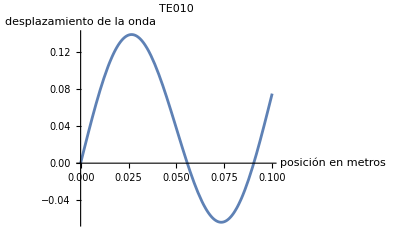

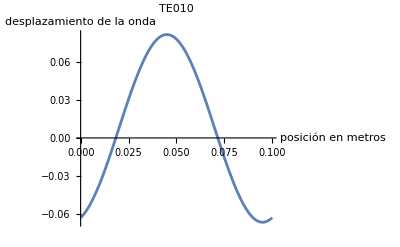

```mathematica
Plot[desplazamientox, {x,0,d}, AxesLabel-> {"posición en  metros","desplazamiento de la onda"  }, PlotLabel-> "TE010"]
Plot[desplazamientoy, {y,0,d}, AxesLabel-> {"posición en metros","desplazamiento de la onda"  }, PlotLabel-> "TE010"]
```

#### Calculo el desplazamiento de una onda e . m (TM010) en las coordenada espacial x y en la coordenada espacial y .

```mathematica
cl=(1/d)*(t/2- (d/4*l*Pi)*(Sin[(2*Pi*l/d)*(x+t)]- Sin[2*l*Pi*x/d]));
dl =(1/d)*(t/2+ (d/4*l*Pi)*(Sin[(2*Pi*l/d)*(x+t)]- Sin[2*l*Pi*h/d]));
```

```mathematica
despx = ((epr-1)*((a^2/pnm)*(l*Pi/d)^2*cl+ dl))/((a/pnm)^2*(l*Pi/d)^2+1);
```

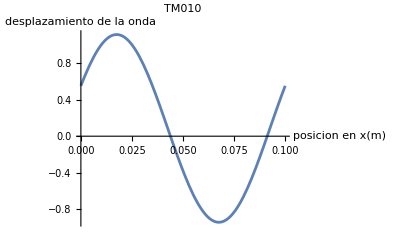

```mathematica
Plot[despx, {x,0,d}, AxesLabel-> {"posicion en x(m)","desplazamiento de la onda"  }, PlotLabel-> "TM010"]
```